## js

```mathematica
<<ASTRAInterpret`
```

```mathematica
phase=-10;
```

```mathematica
FileNames["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\EBT*.sdds"]
```

{\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-BA1-COFFIN-BEG.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-BA1-COFFIN-FOC.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-BA1-DIA-YAG-01.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-BA1-LASERBOX-BEG.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-BA1-LASERBOX-END.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-FCUP-02.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-ICT-03.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-YAG-05.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-YAG-06.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-YAG-07.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-YAG-08.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-DIA-YAG-10.SDDS,\\apclara1\jkj62\Github\OnlineModel\SimulationFramework\Examples\CLARA_FE\CLARA_BA1_Gaussian\TOMP_Sc_-10\EBT-INJ-PSS-SHUT-02.SDDS}

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\CLA-C2V-MARK-01.sdds",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {x, xp, y, yp, t, p, dt, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, IDSlotsPerBunch, SampledCharge, SampledParticles, Pass, PassLength, PassCentralTime, ElapsedTime, ElapsedCoreTime, MemoryUsage, s}

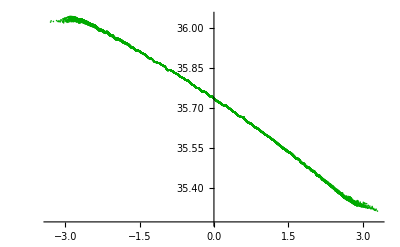

```mathematica
eleplotbefore=ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All,PlotStyle->Darker[Green]]
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\CLA-C2V-MARK-02.sdds",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {x, xp, y, yp, t, p, dt, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, IDSlotsPerBunch, SampledCharge, SampledParticles, Pass, PassLength, PassCentralTime, ElapsedTime, ElapsedCoreTime, MemoryUsage, s}

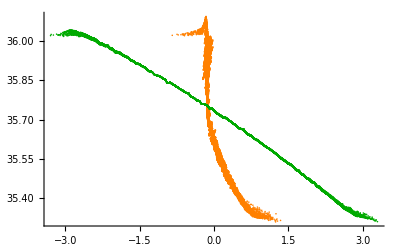

```mathematica
eleplotafter=Show[ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All,PlotStyle->Orange],eleplotbefore,PlotRange->All]
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\EBT-INJ-DIA-YAG-10.sdds",sddsVerbose->True]
```

Number of Pages: 1;	Current Page(s): {1}

Variables (Re)Assigned: {x, xp, y, yp, t, p, dt, particleID}

Parameters (Re)Assigned: {Step, pCentral, Charge, Particles, IDSlotsPerBunch, SampledCharge, SampledParticles, Pass, PassLength, PassCentralTime, ElapsedTime, ElapsedCoreTime, MemoryUsage, s}

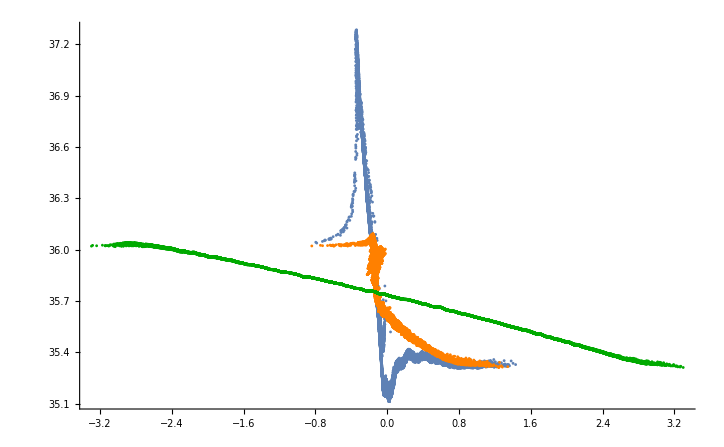

```mathematica
eleplot=Show[ListPlot[{Transpose[{10^12(t-Mean[t]),0.511p}]},PlotRange->All],eleplotafter,PlotRange->All]
```

```mathematica
ASTRABeamInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_ASTRA_"<>ToString[phase]<>"\\S02.1824.001",ASTRAVerbose->True]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

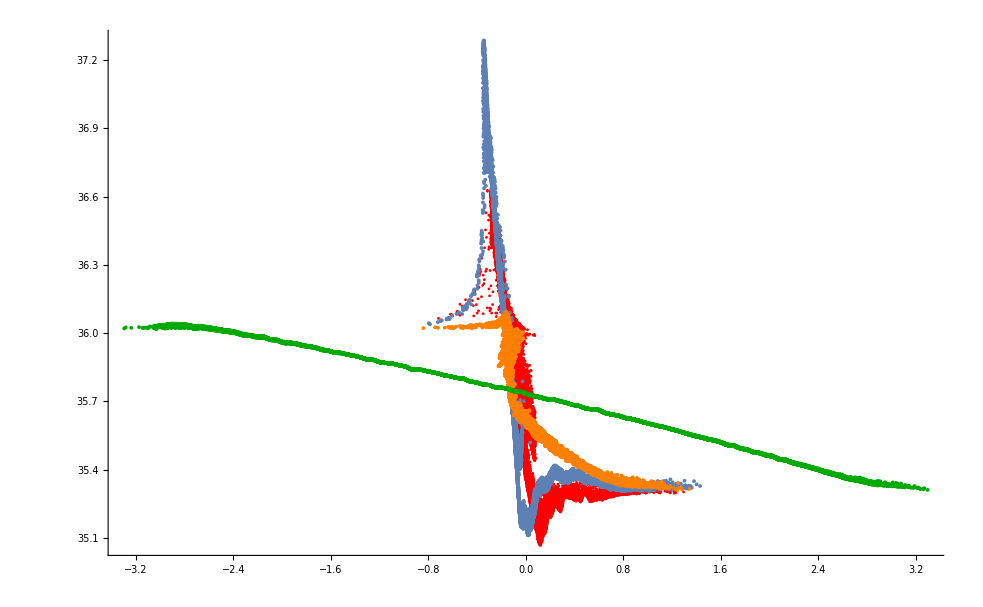

```mathematica
Show[ListPlot[{Transpose[{-10^12(z-Mean[z])/(3 10^8),10^-6 pz}]},PlotRange->All,PlotStyle->{{Red,AbsolutePointSize[2]}}],eleplot,PlotRange->All]
```

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\S02.sig",sddsVerbose->False];
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\S02.flr",sddsVerbose->False];
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_Sc_"<>ToString[phase]<>"\\S02.twi",sddsVerbose->False];
```

```mathematica
s02files=FileNames[("S02."|"VELA."|"BA1.")~~DigitCharacter..~~".001",{"\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_ASTRA_"<>ToString[phase]<>"\\"}];
```

```mathematica
4096^(1/3)
```

16

```mathematica
s02energyspread=Block[{},
ASTRABeamInterpret[#];
{Mean[z],StandardDeviation[pz]/Mean[pz]}
]&/@s02files
```

{{3.59917,0.00488115},{4.08886,0.00489601},{5.00985,0.00492116},{5.72589,0.00493858},{6.40524,0.00847988},{6.98091,0.00856214},{7.59779,0.00530392},{7.8308,0.00551955},{9.53881,0.00682366},{9.88881,0.00706307},{10.5353,0.00748635},{12.0888,0.00844528},{13.9108,0.00949516},{15.5888,0.0104328},{17.1388,0.0112599},{18.2438,0.0118113},{21.2703,0.0131712},{21.3878,0.0132189},{23.0663,0.013833},{23.6838,0.0140127},{24.3338,0.0141775},{24.4338,0.0142009},{25.4848,0.0144211}}

```mathematica
ASTRAemitInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_ASTRA_"<>ToString[phase]<>"\\"<>#<>".Xemit.001"&/@{"S02"(*,"C2V","VELA"*)},ASTRAVerbose->True]
```

Columns Redefined: z [m], t [ns], xavr [mm], xrms [mm], xprms [mrad], ϵxnorm [mm mrad π], xxpavr [mm mrad]

Columns Redefined: z [m], t [ns], yavr [mm], yrms [mm], yprms [mrad], ϵynorm [mm mrad π], yypavr [mm mrad]

Columns Redefined: z [m], t [ns], Ekin [MeV], zrms [mm], ΔErms [keV], ϵznorm [keV mm π], zEavr [keV]

```mathematica
Max[z]
```

25.485

```mathematica
2^4
```

16

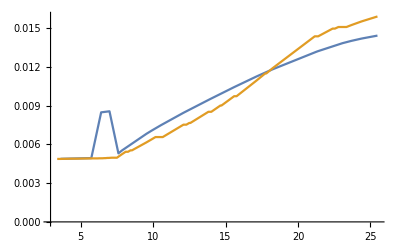

```mathematica
ListLinePlot[{Sort[s02energyspread],Transpose[{Z,Sdelta}]},PlotRange->{All,All}]
```

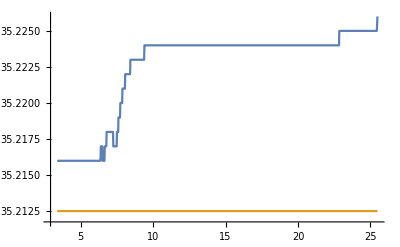

```mathematica
ListLinePlot[{Transpose[{z,Ekin}],Transpose[{Z,(0.511*pCentral0-0.511)}]},PlotRange->{All,All}]
```

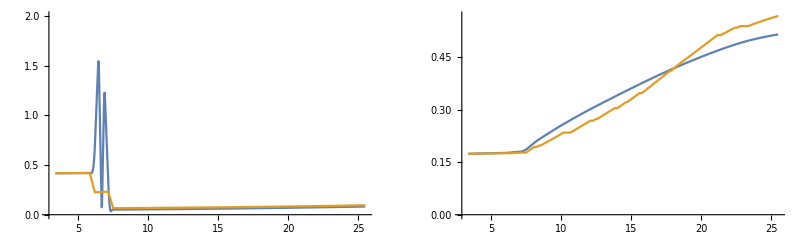

```mathematica
GraphicsRow[{
ListLinePlot[{Transpose[{z,zrms}],Transpose[{Z,10^3 St 3 10^8}]},PlotRange->{All,{0,2}}],
ListLinePlot[{Transpose[{z,10^-3 ΔErms}],Transpose[{Z,Sdelta*0.511*pCentral0}]},PlotRange->{All,All}]
}]
```

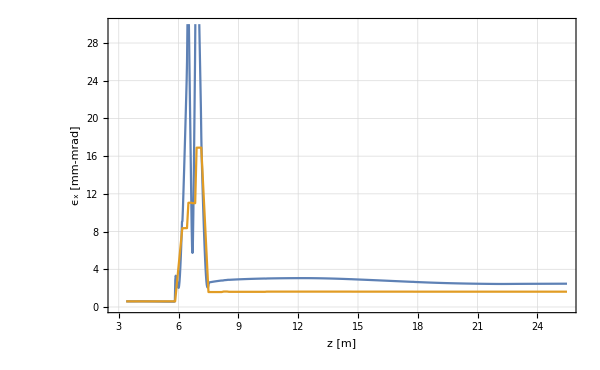

```mathematica
ListLinePlot[{Transpose[{z,ϵxnorm}],Transpose[{Z,10^6 enx}]},PlotRange->{All,{0,30}},PlotTheme->"Detailed",FrameLabel->{"z [m]","ϵ_x [mm-mrad]"},BaseStyle->{FontSize->14},ImageSize->600]
```

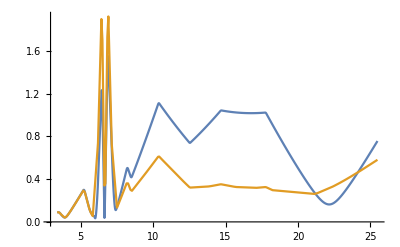

```mathematica
ListLinePlot[{Transpose[{z,xrms}],Transpose[{Z,10^3 Sx}]},PlotRange->All]
```

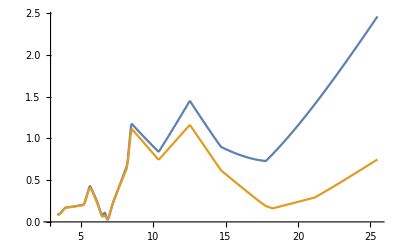

```mathematica
ListLinePlot[{Transpose[{z,yrms}],Transpose[{Z,10^3 Sy}]},PlotRange->All]
```

## HDF5

```mathematica
sddsInterpret["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_SETUP\\CLA-C2V-MARK-02.sdds"]
```

```mathematica
Import["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_ASTRA_-10\\C2V-DIA-SCR-01.hdf5"]
```

{/Parameters/Rotation,/Parameters/Source,/Parameters/Starting_Position,/Parameters/centered,/Parameters/code,/Parameters/npart,/Parameters/particle_mass,/Parameters/total_charge,/beam/beam,/beam/columns,/beam/longitudinal_reference,/beam/units}

```mathematica
Import["\\\\apclara1\\jkj62\\Github\\OnlineModel\\SimulationFramework\\Examples\\CLARA_FE\\CLARA_BA1_Gaussian\\TOMP_ASTRA_-10\\C2V-DIA-SCR-01.hdf5",{"/beam/beam"}]
```

{{-5.60476,4.96201×10^-7,4.26942,21310.1,43.0561,3.57357×10^7,5.41832×10^-9,1.36444×10^-13},{-5.6072,-0.0000176757,4.26983,220375.,-2436.84,3.60371×10^7,5.41696×10^-9,1.36444×10^-13},{-5.60574,0.0000330319,4.26955,101474.,7052.73,3.58455×10^7,5.4179×10^-9,1.36444×10^-13},{-5.60389,4.04509×10^-6,4.26931,-52055.4,6232.97,3.56427×10^7,5.41871×10^-9,1.36444×10^-13},{-5.60211,0.0000792117,4.26905,-208857.,11997.1,3.54187×10^7,5.41958×10^-9,1.36444×10^-13},{-5.60426,0.0000328965,4.26934,-20168.6,7778.06,3.56704×10^7,5.4186×10^-9,1.36444×10^-13},{-5.60424,-4.62619×10^-6,4.26929,-19062.9,111.388,3.56481×10^7,5.41876×10^-9,1.36444×10^-13},{-5.60652,0.0000211307,4.26972,159175.,2162.85,3.59455×10^7,5.41732×10^-9,1.36444×10^-13},{-5.60695,-5.01989×10^-6,4.26979,192334.,-267.381,3.60067×10^7,5.4171×10^-9,1.36444×10^-13},{-5.60173,-0.0000915566,4.26902,-245430.,-12696.5,3.53809×10^7,5.41967×10^-9,1.36444×10^-13},{-5.60342,0.000044594,4.26929,-94831.3,6436.3,3.56129×10^7,5.41876×10^-9,1.36444×10^-13},{-5.60606,0.0000156129,4.26963,125064.,642.797,3.58987×10^7,5.41762×10^-9,1.36444×10^-13},{-5.60483,1.64339×10^-6,4.26942,27004.3,-3145.05,3.57313×10^7,5.41833×10^-9,1.36444×10^-13},{-5.60527,0.0000420502,4.26954,61547.8,5417.54,3.58189×10^7,5.41793×10^-9,1.36444×10^-13},{-5.60426,0.0000789122,4.26931,-17875.5,18022.8,3.56646×10^7,5.41871×10^-9,1.36444×10^-13},{-5.60317,-4.93124×10^-6,4.26919,-114626.,-4137.12,3.5534×10^7,5.41909×10^-9,1.36444×10^-13},{-5.60628,0.0000237157,4.26968,141624.,8072.27,3.592×10^7,5.41747×10^-9,1.36444×10^-13},{-5.60124,0.000146671,4.26896,-294945.,20786.1,3.5326×10^7,5.41987×10^-9,1.36444×10^-13},{-5.60616,-0.0000149047,4.26965,131721.,-5675.55,3.5904×10^7,5.41756×10^-9,1.36444×10^-13},{-5.60161,0.000301379,4.26898,-255389.,44023.1,3.53724×10^7,5.4198×10^-9,1.36444×10^-13},{-5.60322,-2.88622×10^-6,4.26926,-113003.,-1586.05,3.55682×10^7,5.41886×10^-9,1.36444×10^-13},{-5.60623,0.00001788,4.26965,138359.,4418.43,3.59104×10^7,5.41756×10^-9,1.36444×10^-13},{-5.60333,-0.0000130803,4.2692,-99150.9,-2707.29,3.55477×10^7,5.41907×10^-9,1.36444×10^-13},{-5.60631,0.0000167816,4.26966,145595.,7189.7,3.59181×10^7,5.41754×10^-9,1.36444×10^-13},{-5.60654,-0.0000420132,4.26972,160427.,-9782.62,3.59469×10^7,5.41732×10^-9,1.36444×10^-13},{-5.60365,-9.46331×10^-6,4.26929,-73220.5,-5900.9,3.56304×10^7,5.41875×10^-9,1.36444×10^-13},{-5.60465,0.0000613592,4.2694,12788.8,15880.7,3.57162×10^7,5.41839×10^-9,1.36444×10^-13},{-5.60269,-0.000041287,4.26907,-153192.,-6999.93,3.54729×10^7,5.41949×10^-9,1.36444×10^-13},{-5.6051,5.76742×10^-6,4.2694,52717.5,2529.03,3.57392×10^7,5.41839×10^-9,1.36444×10^-13},{-5.60696,0.000166219,4.2698,192155.,24376.5,3.6006×10^7,5.41706×10^-9,1.36444×10^-13},{-5.60275,0.0000279831,4.2692,-154808.,3288.55,3.55236×10^7,5.41905×10^-9,1.36444×10^-13},{-5.60223,-0.0000107976,4.26908,-197977.,114.243,3.54407×10^7,5.41946×10^-9,1.36444×10^-13},{-5.60428,-0.0000218104,4.26935,-18359.4,-8785.17,3.56868×10^7,5.41857×10^-9,1.36444×10^-13},{-5.60572,-0.0000716012,4.26958,98356.2,-7682.88,3.58529×10^7,5.41779×10^-9,1.36444×10^-13},{-5.60281,0.0000662433,4.26915,-144696.,7312.98,3.55086×10^7,5.41924×10^-9,1.36444×10^-13},{-5.60329,-0.000029944,4.2692,-102784.,-1532.04,3.55533×10^7,5.41905×10^-9,1.36444×10^-13},{-5.60626,-0.0000356525,4.26967,140364.,-3018.13,3.59111×10^7,5.41751×10^-9,1.36444×10^-13},{-5.60461,0.000026621,4.26942,8875.37,354.228,3.5733×10^7,5.41832×10^-9,1.36444×10^-13},{-5.60363,-0.0000145832,4.26929,-74170.6,-3446.04,3.56178×10^7,5.41878×10^-9,1.36444×10^-13},{-5.60514,0.0000492883,4.26947,52937.3,6122.13,3.57756×10^7,5.41816×10^-9,1.36444×10^-13},{-5.60241,0.0000735785,4.26911,-182857.,14436.5,3.54785×10^7,5.41937×10^-9,1.36444×10^-13},{-5.60442,-0.0000403588,4.26934,-5045.02,-11462.4,3.56792×10^7,5.4186×10^-9,1.36444×10^-13},{-5.6021,-0.000143199,4.26904,-210867.,-19626.2,3.54114×10^7,5.41959×10^-9,1.36444×10^-13},{-5.60493,-0.000155451,4.26938,39532.5,-29733.2,3.57139×10^7,5.41848×10^-9,1.36444×10^-13},{-5.60691,0.00010322,4.26977,191803.,16001.3,3.6008×10^7,5.41717×10^-9,1.36444×10^-13},{-5.60626,-0.0000266245,4.26966,141301.,-3503.54,3.59168×10^7,5.41753×10^-9,1.36444×10^-13},{-5.60699,-0.000108107,4.26976,199871.,-16092.5,3.5997×10^7,5.4172×10^-9,1.36444×10^-13},{-5.60357,-0.0000173377,4.26926,-80475.7,-1893.68,3.55812×10^7,5.41888×10^-9,1.36444×10^-13},{-5.60592,-1.15922×10^-6,4.26954,117684.,-4111.38,3.58557×10^7,5.41792×10^-9,1.36444×10^-13},{-5.60296,-0.0000949979,4.26914,-131844.,-16178.5,3.55008×10^7,5.41926×10^-9,1.36444×10^-13},{-5.60479,-0.0000555111,4.26942,24638.,-6154.26,3.57418×10^7,5.41834×10^-9,1.36444×10^-13},{-5.6031,-0.0000236155,4.26921,-121513.,-141.808,3.55478×10^7,5.41902×10^-9,1.36444×10^-13},{-5.60499,-0.0000135881,4.26939,43174.,-2049.29,3.57203×10^7,5.41843×10^-9,1.36444×10^-13},{-5.60567,-0.0000452304,4.26962,92181.9,-5646.71,3.58581×10^7,5.41766×10^-9,1.36444×10^-13},{-5.60402,3.75522×10^-6,4.26934,-41154.1,-2296.57,3.56604×10^7,5.41861×10^-9,1.36444×10^-13},{-5.60404,0.0000422311,4.26929,-37067.,3405.87,3.56453×10^7,5.41875×10^-9,1.36444×10^-13},{-5.6045,-0.0000349584,4.26947,-5029.73,-8061.81,3.57418×10^7,5.41816×10^-9,1.36444×10^-13},{-5.60653,-0.0000229076,4.26975,158307.,-6569.56,3.59562×10^7,5.41722×10^-9,1.36444×10^-13},{-5.60222,0.000097019,4.26909,-199806.,15648.5,3.54633×10^7,5.41942×10^-9,1.36444×10^-13},{-5.60288,0.0000492208,4.26915,-138953.,9130.44,3.55117×10^7,5.41923×10^-9,1.36444×10^-13},{-5.60573,0.0000385298,4.26951,102420.,8951.27,3.58172×10^7,5.41803×10^-9,1.36444×10^-13},{-5.6027,-0.0000345208,4.2691,-153208.,-7890.13,3.54926×10^7,5.41939×10^-9,1.36444×10^-13},{-5.60494,0.0000337467,4.26945,37765.,5134.35,3.57509×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60252,0.0000733447,4.26908,-170687.,12115.1,3.54548×10^7,5.41945×10^-9,1.36444×10^-13},{-5.6044,0.000126471,4.26944,-13718.1,25701.1,3.57065×10^7,5.41826×10^-9,1.36444×10^-13},{-5.60442,0.0000577713,4.26938,-6607.69,4274.22,3.56856×10^7,5.41846×10^-9,1.36444×10^-13},{-5.60525,0.0000551322,4.26951,61031.6,15441.3,3.57934×10^7,5.41804×10^-9,1.36444×10^-13},{-5.60473,0.000121626,4.26939,20734.1,26265.,3.57135×10^7,5.41842×10^-9,1.36444×10^-13},{-5.60603,0.0000640349,4.26964,121933.,7659.29,3.59004×10^7,5.41759×10^-9,1.36444×10^-13},{-5.60664,0.0000944658,4.26973,169846.,17675.4,3.59703×10^7,5.4173×10^-9,1.36444×10^-13},{-5.60387,0.000103209,4.26934,-55470.,21232.6,3.56453×10^7,5.41861×10^-9,1.36444×10^-13},{-5.60397,1.86665×10^-6,4.26925,-41123.8,2963.22,3.56156×10^7,5.4189×10^-9,1.36444×10^-13},{-5.6038,-0.0000669722,4.26925,-58473.7,-9240.63,3.55986×10^7,5.4189×10^-9,1.36444×10^-13},{-5.60662,0.000059982,4.2697,168283.,9634.84,3.59516×10^7,5.41739×10^-9,1.36444×10^-13},{-5.60527,0.0000376411,4.26945,64993.7,4697.8,3.57657×10^7,5.41822×10^-9,1.36444×10^-13},{-5.60414,-0.0000215415,4.26924,-25340.4,-3516.86,3.56314×10^7,5.41892×10^-9,1.36444×10^-13},{-5.60427,-0.0000387398,4.26932,-17874.8,-1881.29,3.56555×10^7,5.41865×10^-9,1.36444×10^-13},{-5.60483,-0.0000139929,4.26934,33591.,536.179,3.57062×10^7,5.41861×10^-9,1.36444×10^-13},{-5.603,0.0000862605,4.2692,-129702.,16917.,3.55415×10^7,5.41906×10^-9,1.36444×10^-13},{-5.60583,-0.0000412346,4.26954,110589.,-2799.35,3.58456×10^7,5.41794×10^-9,1.36444×10^-13},{-5.60227,0.0000298574,4.26908,-195095.,1791.06,3.54323×10^7,5.41948×10^-9,1.36444×10^-13},{-5.60333,0.000042589,4.26919,-98271.2,3455.94,3.55471×10^7,5.41909×10^-9,1.36444×10^-13},{-5.60365,-0.000035649,4.26928,-73245.6,-3009.38,3.55976×10^7,5.4188×10^-9,1.36444×10^-13},{-5.60577,0.0000729111,4.26948,109801.,15699.3,3.58291×10^7,5.41812×10^-9,1.36444×10^-13},{-5.60553,0.0000147526,4.26955,82981.8,3404.99,3.58379×10^7,5.41789×10^-9,1.36444×10^-13},{-5.60682,-0.0000906763,4.26972,186370.,-14085.3,3.59673×10^7,5.41733×10^-9,1.36444×10^-13},{-5.60396,-0.0000152887,4.2693,-44434.4,-6497.34,3.56485×10^7,5.41874×10^-9,1.36444×10^-13},{-5.60279,-0.0000169316,4.26919,-150859.,-5660.84,3.5513×10^7,5.4191×10^-9,1.36444×10^-13},{-5.60439,0.000015796,4.2694,-9809.45,7229.,3.5701×10^7,5.41841×10^-9,1.36444×10^-13},{-5.60566,0.000104818,4.26958,93527.7,23096.5,3.58449×10^7,5.4178×10^-9,1.36444×10^-13},{-5.60496,-0.0000210248,4.26946,38698.1,1647.48,3.57682×10^7,5.4182×10^-9,1.36444×10^-13},{-5.60662,-0.0000454148,4.26977,164205.,-7363.12,3.59781×10^7,5.41715×10^-9,1.36444×10^-13},{-5.60382,-0.0000101275,4.26927,-55802.4,960.545,3.56038×10^7,5.41883×10^-9,1.36444×10^-13},{-5.60515,-0.000128897,4.26949,52481.5,-28031.9,3.57872×10^7,5.41809×10^-9,1.36444×10^-13},{-5.60416,-7.78431×10^-6,4.26929,-25866.,3243.27,3.56442×10^7,5.41877×10^-9,1.36444×10^-13},{-5.60603,-0.0000865108,4.26961,123189.,-19736.9,3.58623×10^7,5.41769×10^-9,1.36444×10^-13},{-5.60401,0.0000743751,4.26937,-44215.4,14452.4,3.56653×10^7,5.4185×10^-9,1.36444×10^-13},{-5.60536,0.0000344526,4.26953,69214.,-184.253,3.58072×10^7,5.41796×10^-9,1.36444×10^-13},{-5.60213,0.0000616038,4.26909,-208795.,6636.86,3.54453×10^7,5.41944×10^-9,1.36444×10^-13},{-5.60364,-0.0000449771,4.26923,-71564.7,-4130.89,3.55842×10^7,5.41898×10^-9,1.36444×10^-13},{-5.60584,0.0000284052,4.26957,109871.,4346.24,3.58481×10^7,5.41783×10^-9,1.36444×10^-13},{-5.60616,0.0000433,4.26963,133306.,10746.2,3.58958×10^7,5.41763×10^-9,1.36444×10^-13},{-5.605,-0.0000226307,4.26947,40376.,1338.86,3.57654×10^7,5.41817×10^-9,1.36444×10^-13},{-5.606,-3.5943×10^-6,4.26957,123768.,-4792.59,3.58594×10^7,5.41783×10^-9,1.36444×10^-13},{-5.60448,0.0000122651,4.26942,-3690.94,-693.008,3.57245×10^7,5.41833×10^-9,1.36444×10^-13},{-5.60399,-0.0000450958,4.26928,-42044.6,-7296.7,3.56191×10^7,5.41879×10^-9,1.36444×10^-13},{-5.60314,1.05171×10^-6,4.26924,-119017.,-1068.,3.55688×10^7,5.41892×10^-9,1.36444×10^-13},{-5.6022,0.0000143407,4.26908,-200833.,3166.43,3.54366×10^7,5.41948×10^-9,1.36444×10^-13},{-5.60509,0.0000224559,4.26945,49377.2,8556.23,3.57505×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60283,-0.0000453715,4.26921,-147119.,-8284.65,3.55369×10^7,5.41903×10^-9,1.36444×10^-13},{-5.60506,0.0000179408,4.26948,45957.4,7160.02,3.57797×10^7,5.41814×10^-9,1.36444×10^-13},{-5.6059,-0.0000258775,4.2696,111911.,-4471.9,3.58592×10^7,5.41774×10^-9,1.36444×10^-13},{-5.60213,0.0000657622,4.26909,-208444.,7164.5,3.54425×10^7,5.41944×10^-9,1.36444×10^-13},{-5.60465,0.0000165331,4.26933,16871.5,3544.12,3.56852×10^7,5.41862×10^-9,1.36444×10^-13},{-5.60279,-0.000141617,4.26917,-150206.,-25688.1,3.55049×10^7,5.41915×10^-9,1.36444×10^-13},{-5.60425,0.0000361095,4.26941,-24738.8,6556.55,3.57079×10^7,5.41835×10^-9,1.36444×10^-13},{-5.6059,0.0000419825,4.26958,114180.,7382.09,3.58528×10^7,5.41781×10^-9,1.36444×10^-13},{-5.60358,6.87342×10^-6,4.2693,-80523.2,4105.15,3.56278×10^7,5.41873×10^-9,1.36444×10^-13},{-5.60481,0.0000534914,4.26952,19739.,9852.95,3.57701×10^7,5.41798×10^-9,1.36444×10^-13},{-5.60477,0.0000285411,4.26935,25892.8,2917.18,3.5714×10^7,5.41856×10^-9,1.36444×10^-13},{-5.60512,-0.0000327785,4.2695,50423.3,728.496,3.57891×10^7,5.41807×10^-9,1.36444×10^-13},{-5.6057,0.0000343376,4.26955,97555.7,11012.1,3.5842×10^7,5.4179×10^-9,1.36444×10^-13},{-5.60305,0.0000215327,4.26917,-124795.,2166.57,3.55171×10^7,5.41917×10^-9,1.36444×10^-13},{-5.60396,-0.0000560228,4.26931,-46033.5,-15431.9,3.5641×10^7,5.41869×10^-9,1.36444×10^-13},{-5.60433,6.00797×10^-6,4.26941,-16478.7,3215.16,3.5713×10^7,5.41837×10^-9,1.36444×10^-13},{-5.60245,0.0000143652,4.2691,-176663.,3994.29,3.54801×10^7,5.4194×10^-9,1.36444×10^-13},{-5.60463,0.0000294633,4.26941,10140.8,11402.3,3.57314×10^7,5.41835×10^-9,1.36444×10^-13},{-5.6061,-0.0000116742,4.26964,127667.,-5945.61,3.59032×10^7,5.4176×10^-9,1.36444×10^-13},{-5.60462,0.0000807833,4.26947,6561.3,16651.,3.57483×10^7,5.41818×10^-9,1.36444×10^-13},{-5.6034,0.0000484119,4.26928,-97361.1,11589.2,3.55915×10^7,5.4188×10^-9,1.36444×10^-13},{-5.60181,0.0000572138,4.26902,-237889.,6173.75,3.53905×10^7,5.41965×10^-9,1.36444×10^-13},{-5.60515,-0.0000164877,4.26948,53044.6,-18.1286,3.57784×10^7,5.41814×10^-9,1.36444×10^-13},{-5.60538,6.36991×10^-6,4.26953,70970.2,1506.55,3.58052×10^7,5.41797×10^-9,1.36444×10^-13},{-5.60542,0.0000514718,4.26954,74701.1,7416.3,3.58305×10^7,5.41793×10^-9,1.36444×10^-13},{-5.60546,-0.000061322,4.26949,79659.4,-7194.28,3.58029×10^7,5.4181×10^-9,1.36444×10^-13},{-5.60503,6.41366×10^-6,4.26935,50708.3,-278.358,3.57369×10^7,5.41856×10^-9,1.36444×10^-13},{-5.60202,-5.30223×10^-6,4.26903,-216180.,-1556.96,3.54147×10^7,5.41964×10^-9,1.36444×10^-13},{-5.60622,-0.0000283378,4.26967,136780.,-2683.5,3.59089×10^7,5.4175×10^-9,1.36444×10^-13},{-5.6068,-0.0000397577,4.26973,184524.,-8909.33,3.59833×10^7,5.4173×10^-9,1.36444×10^-13},{-5.60357,-0.0000781365,4.26928,-81918.8,-18026.2,3.56032×10^7,5.41878×10^-9,1.36444×10^-13},{-5.60507,0.000028024,4.26935,54935.3,6427.15,3.57411×10^7,5.41855×10^-9,1.36444×10^-13},{-5.60458,-0.0000748254,4.2694,6572.25,-10113.2,3.5707×10^7,5.4184×10^-9,1.36444×10^-13},{-5.60293,-3.42388×10^-6,4.26909,-129670.,736.896,3.54927×10^7,5.41945×10^-9,1.36444×10^-13},{-5.6068,0.000141872,4.26982,178178.,23099.7,3.60008×10^7,5.41701×10^-9,1.36444×10^-13},{-5.6045,-0.00003212,4.2693,5009.98,-7366.01,3.56819×10^7,5.41873×10^-9,1.36444×10^-13},{-5.60474,-0.0000138183,4.26945,18126.1,3749.94,3.57346×10^7,5.41824×10^-9,1.36444×10^-13},{-5.60305,-0.0000330606,4.26916,-122886.,-4561.95,3.5528×10^7,5.41919×10^-9,1.36444×10^-13},{-5.60225,-0.0000448842,4.26909,-197627.,-5980.67,3.54387×10^7,5.41944×10^-9,1.36444×10^-13},{-5.6034,0.000172375,4.26923,-93338.3,32521.1,3.5585×10^7,5.41897×10^-9,1.36444×10^-13},{-5.60595,0.0000611573,4.26956,119597.,13020.9,3.58551×10^7,5.41787×10^-9,1.36444×10^-13},{-5.6048,0.0000273691,4.26938,27102.7,7489.53,3.57026×10^7,5.41847×10^-9,1.36444×10^-13},{-5.60709,0.000334135,4.26976,212399.,54613.5,3.60253×10^7,5.41718×10^-9,1.36444×10^-13},{-5.60642,0.000122794,4.2697,153091.,24306.1,3.59472×10^7,5.41738×10^-9,1.36444×10^-13},{-5.60428,0.000023644,4.26937,-18344.9,3850.23,3.56833×10^7,5.41851×10^-9,1.36444×10^-13},{-5.60471,0.000061566,4.26942,16765.4,8613.19,3.57316×10^7,5.41832×10^-9,1.36444×10^-13},{-5.60489,8.07429×10^-6,4.26946,31170.8,-2366.79,3.57559×10^7,5.41821×10^-9,1.36444×10^-13},{-5.60271,0.0000658491,4.26915,-154886.,11686.6,3.55059×10^7,5.41924×10^-9,1.36444×10^-13},{-5.60631,-0.000082481,4.26968,144268.,-11842.9,3.59297×10^7,5.41746×10^-9,1.36444×10^-13},{-5.60488,0.0000530989,4.26946,30190.2,4266.81,3.57645×10^7,5.41818×10^-9,1.36444×10^-13},{-5.60359,7.61517×10^-6,4.26922,-75507.4,-2814.91,3.55794×10^7,5.419×10^-9,1.36444×10^-13},{-5.60606,3.82295×10^-6,4.26963,126694.,-2722.1,3.58987×10^7,5.41763×10^-9,1.36444×10^-13},{-5.6072,-0.000152663,4.26991,205335.,-25025.,3.60348×10^7,5.41671×10^-9,1.36444×10^-13},{-5.60385,0.0000114553,4.2693,-55110.8,2506.54,3.56447×10^7,5.41872×10^-9,1.36444×10^-13},{-5.60518,-7.09237×10^-6,4.26938,62958.7,329.615,3.57337×10^7,5.41847×10^-9,1.36444×10^-13},{-5.60575,-5.29369×10^-6,4.26958,101276.,4240.69,3.58506×10^7,5.4178×10^-9,1.36444×10^-13},{-5.60134,0.00109194,4.26886,-273439.,153480.,3.53631×10^7,5.4202×10^-9,1.36444×10^-13},{-5.60432,0.00005208,4.2694,-16313.2,5464.36,3.56978×10^7,5.4184×10^-9,1.36444×10^-13},{-5.60272,0.0000428612,4.26915,-155244.,7460.16,3.54987×10^7,5.41924×10^-9,1.36444×10^-13},{-5.60573,-0.0000421017,4.26959,98091.6,-4360.01,3.5856×10^7,5.41777×10^-9,1.36444×10^-13},{-5.60655,-0.0000395253,4.26975,160152.,-5617.48,3.59653×10^7,5.41724×10^-9,1.36444×10^-13},{-5.60395,-0.0000103969,4.26924,-43023.8,-3161.3,3.56138×10^7,5.41893×10^-9,1.36444×10^-13},{-5.60293,3.27292×10^-7,4.26918,-136472.,-3781.35,3.5511×10^7,5.41915×10^-9,1.36444×10^-13},{-5.60225,-0.000105406,4.26909,-197668.,-18911.1,3.54566×10^7,5.41942×10^-9,1.36444×10^-13},{-5.60629,0.0000559208,4.26968,143971.,13460.5,3.59245×10^7,5.41748×10^-9,1.36444×10^-13},{-5.6019,-0.0000557005,4.26902,-227772.,-9435.2,3.53989×10^7,5.41967×10^-9,1.36444×10^-13},{-5.60246,0.0000597148,4.2691,-177930.,11111.8,3.54726×10^7,5.41939×10^-9,1.36444×10^-13},{-5.6025,-9.9692×10^-7,4.26913,-175193.,1030.3,3.5473×10^7,5.41929×10^-9,1.36444×10^-13},{-5.60465,0.000095091,4.26947,8812.38,20827.6,3.57466×10^7,5.41818×10^-9,1.36444×10^-13},{-5.6042,0.0000335252,4.26927,-21485.2,6902.18,3.56228×10^7,5.41882×10^-9,1.36444×10^-13},{-5.60651,-0.0000506825,4.26973,159224.,-5657.44,3.59574×10^7,5.41731×10^-9,1.36444×10^-13},{-5.60532,-4.05845×10^-6,4.26947,68133.,381.319,3.57805×10^7,5.41816×10^-9,1.36444×10^-13},{-5.60522,0.0000594149,4.26945,61111.6,14903.1,3.57653×10^7,5.41823×10^-9,1.36444×10^-13},{-5.6052,-3.08166×10^-6,4.26951,55790.5,-6913.81,3.57861×10^7,5.41803×10^-9,1.36444×10^-13},{-5.6072,0.000257801,4.26988,208150.,41403.5,3.60371×10^7,5.4168×10^-9,1.36444×10^-13},{-5.6044,0.0000387133,4.26939,-8408.41,4781.02,3.56976×10^7,5.41843×10^-9,1.36444×10^-13},{-5.60457,-0.0000127479,4.26935,7341.16,-949.254,3.56992×10^7,5.41856×10^-9,1.36444×10^-13},{-5.60556,-0.0000138698,4.26953,86213.4,-7158.23,3.58102×10^7,5.41798×10^-9,1.36444×10^-13},{-5.60594,0.0000291001,4.26962,115501.,11059.8,3.58781×10^7,5.41765×10^-9,1.36444×10^-13},{-5.605,-0.0000310368,4.26949,40125.2,-9240.51,3.57847×10^7,5.41809×10^-9,1.36444×10^-13},{-5.60475,0.0000183167,4.26935,25293.3,6836.89,3.5711×10^7,5.41858×10^-9,1.36444×10^-13},{-5.60593,-0.0000346344,4.26962,116900.,-2929.23,3.5876×10^7,5.41767×10^-9,1.36444×10^-13},{-5.60451,-4.22283×10^-8,4.26938,674.074,1907.29,3.56849×10^7,5.41847×10^-9,1.36444×10^-13},{-5.60521,-1.2032×10^-6,4.26946,60076.3,1908.35,3.57721×10^7,5.41821×10^-9,1.36444×10^-13},{-5.60568,-0.0000206854,4.26954,97642.9,-84.4395,3.58395×10^7,5.41793×10^-9,1.36444×10^-13},{-5.6043,0.0000531626,4.26942,-20502.9,9768.23,3.57138×10^7,5.41832×10^-9,1.36444×10^-13},{-5.60614,-0.0000559257,4.26963,132190.,-13536.4,3.58918×10^7,5.41764×10^-9,1.36444×10^-13},{-5.60518,-0.000113615,4.26942,60066.7,-22475.5,3.57613×10^7,5.41834×10^-9,1.36444×10^-13},{-5.60384,0.0000230554,4.26928,-55250.1,7807.4,3.56061×10^7,5.41881×10^-9,1.36444×10^-13},{-5.60584,-0.0000603112,4.26957,109534.,-5601.49,3.58497×10^7,5.41782×10^-9,1.36444×10^-13},{-5.60466,-0.0000105482,4.2694,13310.7,-4054.7,3.57184×10^7,5.41839×10^-9,1.36444×10^-13},{-5.60291,0.0000413879,4.26919,-139179.,5421.86,3.55182×10^7,5.41911×10^-9,1.36444×10^-13},{-5.60368,-0.0000113069,4.26926,-70017.1,-7005.49,3.55877×10^7,5.41887×10^-9,1.36444×10^-13},{-5.60647,0.0000137184,4.26967,158871.,2272.17,3.59262×10^7,5.4175×10^-9,1.36444×10^-13},{-5.60608,0.0000318983,4.26965,125199.,2461.53,3.59018×10^7,5.41756×10^-9,1.36444×10^-13},{-5.60422,0.0000537153,4.26933,-23749.2,15070.2,3.56562×10^7,5.41862×10^-9,1.36444×10^-13},{-5.60359,0.0000636978,4.26929,-78756.9,13274.9,3.56191×10^7,5.41877×10^-9,1.36444×10^-13},{-5.60311,-0.00002062,4.26917,-118862.,1132.54,3.55253×10^7,5.41916×10^-9,1.36444×10^-13},{-5.60189,-5.87301×10^-6,4.26905,-231411.,221.252,3.54076×10^7,5.41957×10^-9,1.36444×10^-13},{-5.60239,1.86567×10^-6,4.26909,-182190.,-3246.91,3.54619×10^7,5.41943×10^-9,1.36444×10^-13},{-5.60116,-0.00093168,4.26885,-300791.,-127300.,3.53259×10^7,5.42024×10^-9,1.36444×10^-13},{-5.60392,-7.42642×10^-6,4.26927,-48200.9,-6035.6,3.56031×10^7,5.41883×10^-9,1.36444×10^-13},{-5.60591,0.0000295462,4.26966,111776.,2706.24,3.59001×10^7,5.41754×10^-9,1.36444×10^-13},{-5.60433,-0.0000207345,4.26937,-15079.3,-5717.86,3.56767×10^7,5.41849×10^-9,1.36444×10^-13},{-5.60625,-0.000020304,4.26969,139728.,-4085.05,3.59391×10^7,5.41744×10^-9,1.36444×10^-13},{-5.60705,0.000129122,4.2698,200241.,20791.8,3.60138×10^7,5.41705×10^-9,1.36444×10^-13},{-5.60651,-0.0000139267,4.2697,161577.,-806.54,3.5963×10^7,5.4174×10^-9,1.36444×10^-13},{-5.60661,0.0000729472,4.26972,166852.,11979.,3.59482×10^7,5.41734×10^-9,1.36444×10^-13},{-5.60689,0.000105752,4.26976,190625.,17139.9,3.5997×10^7,5.41719×10^-9,1.36444×10^-13},{-5.60368,-0.000115825,4.26921,-67088.,-22536.8,3.55803×10^7,5.41902×10^-9,1.36444×10^-13},{-5.60428,0.0000498822,4.26938,-20021.4,6110.7,3.56781×10^7,5.41846×10^-9,1.36444×10^-13},{-5.60674,0.0000754631,4.26976,176991.,9274.45,3.5972×10^7,5.41721×10^-9,1.36444×10^-13},{-5.60606,0.0000132673,4.26961,125921.,3995.17,3.58651×10^7,5.41768×10^-9,1.36444×10^-13},{-5.6044,-0.0000528688,4.2694,-10062.7,-6002.46,3.57062×10^7,5.41839×10^-9,1.36444×10^-13},{-5.60542,-6.70663×10^-6,4.26955,74200.9,-1896.59,3.58297×10^7,5.41791×10^-9,1.36444×10^-13},{-5.60395,-0.0000195822,4.26929,-44970.9,2191.98,3.5643×10^7,5.41875×10^-9,1.36444×10^-13},{-5.60275,0.000072498,4.26915,-151720.,11826.1,3.55033×10^7,5.41924×10^-9,1.36444×10^-13},{-5.60522,0.0000692807,4.26945,61085.5,16829.4,3.57627×10^7,5.41824×10^-9,1.36444×10^-13},{-5.60471,-2.12055×10^-6,4.2694,18229.6,687.741,3.57239×10^7,5.41838×10^-9,1.36444×10^-13},{-5.60479,0.000035864,4.26944,23589.3,6302.6,3.57371×10^7,5.41827×10^-9,1.36444×10^-13},{-5.60362,-0.0000316773,4.26922,-72285.3,-519.776,3.55844×10^7,5.41899×10^-9,1.36444×10^-13},{-5.6059,0.0000352186,4.26953,117187.,7441.22,3.58379×10^7,5.41797×10^-9,1.36444×10^-13},{-5.60409,0.0000412416,4.26933,-35650.2,4040.49,3.5638×10^7,5.41865×10^-9,1.36444×10^-13},{-5.60476,-0.0000318456,4.2694,21851.9,1139.15,3.5718×10^7,5.41839×10^-9,1.36444×10^-13},{-5.60361,-9.62978×10^-6,4.26922,-73751.3,106.219,3.55817×10^7,5.41899×10^-9,1.36444×10^-13},{-5.60625,-0.0000451106,4.26966,139995.,-2702.87,3.59114×10^7,5.41752×10^-9,1.36444×10^-13},{-5.6056,-0.0000864027,4.26963,84090.4,-17663.8,3.58653×10^7,5.41762×10^-9,1.36444×10^-13},{-5.60217,0.0000271389,4.26907,-204920.,5628.08,3.54243×10^7,5.41949×10^-9,1.36444×10^-13},{-5.60608,0.0000211729,4.26962,128071.,3824.61,3.58818×10^7,5.41766×10^-9,1.36444×10^-13},{-5.60612,0.0000819565,4.26966,129125.,18129.8,3.59073×10^7,5.41753×10^-9,1.36444×10^-13},{-5.60361,-0.000177265,4.26926,-76854.,-33613.1,3.55853×10^7,5.41886×10^-9,1.36444×10^-13},{-5.60372,-0.000066204,4.26936,-72703.,-11945.5,3.56408×10^7,5.41852×10^-9,1.36444×10^-13},{-5.60648,6.75769×10^-6,4.26977,152532.,-136.937,3.59558×10^7,5.41718×10^-9,1.36444×10^-13},{-5.60311,-0.0000551929,4.26918,-118396.,-4451.57,3.5533×10^7,5.41913×10^-9,1.36444×10^-13},{-5.60494,-0.0000224,4.26944,36634.3,2518.47,3.57438×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60713,0.000158182,4.26991,198125.,24843.5,3.60287×10^7,5.41669×10^-9,1.36444×10^-13},{-5.6062,0.0000453818,4.26969,134252.,5376.81,3.59324×10^7,5.41744×10^-9,1.36444×10^-13},{-5.60399,0.0000978261,4.26924,-38322.8,20723.2,3.56284×10^7,5.41894×10^-9,1.36444×10^-13},{-5.60512,0.0000216584,4.26953,48981.8,3632.11,3.57985×10^7,5.41797×10^-9,1.36444×10^-13},{-5.60166,-9.10902×10^-6,4.26901,-251475.,-1139.07,3.53844×10^7,5.41969×10^-9,1.36444×10^-13},{-5.60332,-0.0000371461,4.26923,-101057.,-9414.99,3.55824×10^7,5.41896×10^-9,1.36444×10^-13},{-5.60311,-2.86687×10^-7,4.26914,-116478.,-3069.45,3.55149×10^7,5.41928×10^-9,1.36444×10^-13},{-5.6024,0.0000551641,4.26909,-182501.,10094.,3.54653×10^7,5.41942×10^-9,1.36444×10^-13},{-5.60322,-0.0000143546,4.26921,-110274.,-5333.76,3.55473×10^7,5.41904×10^-9,1.36444×10^-13},{-5.60385,0.0000978657,4.26939,-61568.,17594.3,3.56508×10^7,5.41844×10^-9,1.36444×10^-13},{-5.60412,0.0000374718,4.26933,-33226.1,1562.83,3.56492×10^7,5.41862×10^-9,1.36444×10^-13},{-5.6027,-0.0000615575,4.26914,-155380.,-9595.52,3.54981×10^7,5.41925×10^-9,1.36444×10^-13},{-5.60267,-0.0000627318,4.26911,-157924.,-12459.9,3.54942×10^7,5.41936×10^-9,1.36444×10^-13},{-5.60562,-0.0000140427,4.26958,90258.1,2606.66,3.58533×10^7,5.41778×10^-9,1.36444×10^-13},{-5.60457,0.000118645,4.26936,7457.06,24874.3,3.56986×10^7,5.41852×10^-9,1.36444×10^-13},{-5.60323,0.0000581953,4.26921,-109676.,13784.2,3.55527×10^7,5.41903×10^-9,1.36444×10^-13},{-5.60274,-0.0000469565,4.26913,-150593.,-6444.36,3.54923×10^7,5.41931×10^-9,1.36444×10^-13},{-5.60513,0.0000540376,4.26948,52001.2,6220.9,3.57804×10^7,5.41814×10^-9,1.36444×10^-13},{-5.60363,0.0000256622,4.26931,-75554.2,5388.34,3.56319×10^7,5.41871×10^-9,1.36444×10^-13},{-5.60256,0.0000872002,4.26906,-165740.,13318.3,3.54603×10^7,5.41952×10^-9,1.36444×10^-13},{-5.60231,-0.000116503,4.26906,-190194.,-19476.9,3.54413×10^7,5.41953×10^-9,1.36444×10^-13},{-5.60588,5.57266×10^-6,4.26954,114592.,-2855.83,3.58494×10^7,5.41793×10^-9,1.36444×10^-13},{-5.60164,0.0000517307,4.26898,-250182.,8468.11,3.5378×10^7,5.41979×10^-9,1.36444×10^-13},{-5.60362,7.48137×10^-6,4.26928,-76169.9,-2162.78,3.56054×10^7,5.41879×10^-9,1.36444×10^-13},{-5.60706,0.0000945801,4.26984,195948.,14467.6,3.60154×10^7,5.41692×10^-9,1.36444×10^-13},{-5.60359,-0.0000316566,4.26926,-76719.9,-5333.41,3.55943×10^7,5.41887×10^-9,1.36444×10^-13},{-5.60597,-0.0000745432,4.26955,123137.,-14863.,3.58613×10^7,5.41791×10^-9,1.36444×10^-13},{-5.6049,-0.0000301848,4.26946,32629.2,-10957.5,3.57578×10^7,5.41821×10^-9,1.36444×10^-13},{-5.60284,0.0000957501,4.2691,-140336.,16628.5,3.54938×10^7,5.4194×10^-9,1.36444×10^-13},{-5.60227,-0.0000607596,4.26906,-194944.,-9457.79,3.54305×10^7,5.41952×10^-9,1.36444×10^-13},{-5.60534,-0.0000483117,4.26953,68149.7,-7255.05,3.58117×10^7,5.41797×10^-9,1.36444×10^-13},{-5.6063,-2.63712×10^-6,4.26968,144204.,-2287.08,3.59303×10^7,5.41747×10^-9,1.36444×10^-13},{-5.60355,0.0000565326,4.26928,-82833.4,6253.06,3.55977×10^7,5.4188×10^-9,1.36444×10^-13},{-5.60452,-0.0000176754,4.26946,-1914.29,-4366.06,3.57364×10^7,5.41821×10^-9,1.36444×10^-13},{-5.60454,-0.0000800794,4.26938,3819.58,-18944.9,3.5694×10^7,5.41846×10^-9,1.36444×10^-13},{-5.60535,0.000159377,4.26955,67506.3,32237.6,3.5827×10^7,5.4179×10^-9,1.36444×10^-13},{-5.60454,-0.0000229053,4.26943,2158.19,-5182.34,3.57277×10^7,5.41828×10^-9,1.36444×10^-13},{-5.60312,0.0000315445,4.26926,-122712.,2798.57,3.55586×10^7,5.41888×10^-9,1.36444×10^-13},{-5.60637,-0.0000472682,4.2697,148391.,-11198.6,3.59484×10^7,5.41741×10^-9,1.36444×10^-13},{-5.60144,-0.000191706,4.26894,-267974.,-26127.5,3.53606×10^7,5.41992×10^-9,1.36444×10^-13},{-5.60184,-0.0000166645,4.26905,-237839.,-1636.05,3.53887×10^7,5.41958×10^-9,1.36444×10^-13},{-5.60578,-0.0000205318,4.26959,102977.,1651.37,3.58622×10^7,5.41776×10^-9,1.36444×10^-13},{-5.60382,-0.0000376219,4.26928,-58249.8,-5521.56,3.56041×10^7,5.4188×10^-9,1.36444×10^-13},{-5.60365,0.000051896,4.26927,-71985.,6613.75,3.56005×10^7,5.41882×10^-9,1.36444×10^-13},{-5.60488,-0.0000787591,4.26944,31250.,-11008.9,3.57413×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60701,-0.000147838,4.26978,199740.,-22701.7,3.60174×10^7,5.41715×10^-9,1.36444×10^-13},{-5.60693,-0.0000220083,4.2698,191375.,-1292.39,3.60046×10^7,5.41706×10^-9,1.36444×10^-13},{-5.60409,-9.82247×10^-6,4.26933,-34542.2,-4415.18,3.56543×10^7,5.41863×10^-9,1.36444×10^-13},{-5.60665,-0.0000749384,4.26977,168841.,-13844.1,3.59807×10^7,5.41716×10^-9,1.36444×10^-13},{-5.60625,-0.0000290725,4.26969,137698.,-9827.79,3.59273×10^7,5.41744×10^-9,1.36444×10^-13},{-5.60495,8.07377×10^-6,4.26948,35761.6,-226.846,3.57712×10^7,5.41813×10^-9,1.36444×10^-13},{-5.6039,0.0000525481,4.26933,-51866.2,13174.2,3.56419×10^7,5.41863×10^-9,1.36444×10^-13},{-5.60472,-0.0000224875,4.26944,17747.9,-1661.14,3.57355×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60631,-0.0000425738,4.26969,143550.,-8177.23,3.59367×10^7,5.41743×10^-9,1.36444×10^-13},{-5.60451,0.000188579,4.26939,962.949,36985.5,3.57034×10^7,5.41842×10^-9,1.36444×10^-13},{-5.60358,0.0000581323,4.26929,-78805.7,9883.34,3.56164×10^7,5.41878×10^-9,1.36444×10^-13},{-5.60216,-0.0000479822,4.2691,-207672.,-9604.38,3.54553×10^7,5.4194×10^-9,1.36444×10^-13},{-5.60439,-9.76122×10^-6,4.2694,-9578.8,1425.8,3.57106×10^7,5.41839×10^-9,1.36444×10^-13},{-5.60527,-0.0000394551,4.26956,59895.1,-4456.69,3.58283×10^7,5.41787×10^-9,1.36444×10^-13},{-5.60691,-0.000102645,4.26976,191453.,-15552.7,3.5987×10^7,5.41721×10^-9,1.36444×10^-13},{-5.60717,-0.0000937202,4.26985,208655.,-14826.4,3.60312×10^7,5.41691×10^-9,1.36444×10^-13},{-5.60344,-0.0000415175,4.26925,-91175.5,-10846.4,3.55852×10^7,5.41891×10^-9,1.36444×10^-13},{-5.60669,0.0000325497,4.26968,178460.,8036.7,3.59638×10^7,5.41745×10^-9,1.36444×10^-13},{-5.60352,-0.0000497916,4.26919,-80766.2,-5003.88,3.55578×10^7,5.41909×10^-9,1.36444×10^-13},{-5.60327,0.0000377401,4.26923,-105045.,5350.35,3.55801×10^7,5.41897×10^-9,1.36444×10^-13},{-5.60517,-0.00005237,4.26948,55647.3,-14560.9,3.57885×10^7,5.41812×10^-9,1.36444×10^-13},{-5.60303,6.22932×10^-6,4.26918,-126440.,2081.54,3.55198×10^7,5.41913×10^-9,1.36444×10^-13},{-5.60685,0.00006996,4.26977,184691.,13627.1,3.59861×10^7,5.41717×10^-9,1.36444×10^-13},{-5.60289,-0.0000128661,4.26916,-139915.,-5524.29,3.55099×10^7,5.4192×10^-9,1.36444×10^-13},{-5.60584,-0.0000139666,4.26961,107079.,1222.68,3.58531×10^7,5.4177×10^-9,1.36444×10^-13},{-5.60421,0.000050404,4.26935,-25087.9,7265.02,3.56829×10^7,5.41857×10^-9,1.36444×10^-13},{-5.60332,0.0000699704,4.26923,-100962.,8563.56,3.55766×10^7,5.41897×10^-9,1.36444×10^-13},{-5.60721,-0.00015625,4.26977,223515.,-25288.7,3.60446×10^7,5.41717×10^-9,1.36444×10^-13},{-5.60358,0.0000408391,4.26927,-79253.9,12097.,3.55919×10^7,5.41883×10^-9,1.36444×10^-13},{-5.60587,0.0000169191,4.26957,111444.,6852.97,3.58505×10^7,5.41782×10^-9,1.36444×10^-13},{-5.60237,-0.000034109,4.26909,-185462.,-5296.67,3.5462×10^7,5.41942×10^-9,1.36444×10^-13},{-5.60215,-0.0000646924,4.26903,-203956.,-7317.23,3.54208×10^7,5.41963×10^-9,1.36444×10^-13},{-5.60152,0.0000719519,4.26902,-269444.,10267.7,3.53623×10^7,5.41966×10^-9,1.36444×10^-13},{-5.60574,0.0000520395,4.26962,99850.5,9556.2,3.58601×10^7,5.41767×10^-9,1.36444×10^-13},{-5.60516,-0.0000304113,4.26954,50463.9,-10117.3,3.58045×10^7,5.41793×10^-9,1.36444×10^-13},{-5.60133,0.000902236,4.26891,-278942.,127302.,3.5354×10^7,5.42004×10^-9,1.36444×10^-13},{-5.60614,-0.0000996812,4.26969,128485.,-21939.,3.59146×10^7,5.41744×10^-9,1.36444×10^-13},{-5.60197,-0.000262741,4.26901,-220716.,-39784.1,3.54074×10^7,5.4197×10^-9,1.36444×10^-13},{-5.60582,-4.43878×10^-6,4.26952,109813.,-1531.81,3.58248×10^7,5.418×10^-9,1.36444×10^-13},{-5.60265,-5.1302×10^-6,4.26919,-164429.,-2439.83,3.5506×10^7,5.41909×10^-9,1.36444×10^-13},{-5.60589,-0.0000559866,4.26953,115230.,-8360.22,3.58423×10^7,5.41795×10^-9,1.36444×10^-13},{-5.60486,-0.0000307598,4.26945,28921.7,-2267.76,3.57386×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60461,-0.0000823802,4.26946,5188.25,-17617.6,3.57463×10^7,5.41818×10^-9,1.36444×10^-13},{-5.60243,0.000088857,4.26907,-178487.,15452.6,3.54523×10^7,5.41951×10^-9,1.36444×10^-13},{-5.60255,8.82035×10^-6,4.26911,-169291.,-2411.03,3.54826×10^7,5.41937×10^-9,1.36444×10^-13},{-5.60386,-0.0000262645,4.26934,-56079.,-4838.47,3.56568×10^7,5.4186×10^-9,1.36444×10^-13},{-5.60239,-0.0000607293,4.26913,-184608.,-7666.17,3.547×10^7,5.41931×10^-9,1.36444×10^-13},{-5.60185,0.0000862539,4.26901,-231616.,14031.9,3.53993×10^7,5.41969×10^-9,1.36444×10^-13},{-5.60601,-6.05431×10^-6,4.26963,121795.,-289.512,3.5902×10^7,5.41762×10^-9,1.36444×10^-13},{-5.60335,-0.000039003,4.26921,-98287.4,-4463.73,3.55599×10^7,5.41902×10^-9,1.36444×10^-13},{-5.6057,-0.0000487256,4.26951,99615.7,-5477.16,3.58132×10^7,5.41804×10^-9,1.36444×10^-13},{-5.60551,-0.0000194874,4.26948,83865.7,-3628.23,3.57977×10^7,5.41813×10^-9,1.36444×10^-13},{-5.60609,3.90095×10^-7,4.26962,129025.,4954.98,3.58879×10^7,5.41766×10^-9,1.36444×10^-13},{-5.60512,4.36599×10^-7,4.26947,50425.2,-4520.7,3.5771×10^7,5.41815×10^-9,1.36444×10^-13},{-5.60559,0.0000213301,4.2695,91379.3,7825.91,3.58093×10^7,5.41808×10^-9,1.36444×10^-13},{-5.60246,-9.36059×10^-6,4.26909,-177202.,-1634.71,3.54531×10^7,5.41942×10^-9,1.36444×10^-13},{-5.60391,-0.0000206127,4.26933,-51191.1,-987.695,3.56476×10^7,5.41861×10^-9,1.36444×10^-13},{-5.60712,-0.000113899,4.26985,200955.,-18455.6,3.60233×10^7,5.41688×10^-9,1.36444×10^-13},{-5.60566,-7.01192×10^-6,4.26956,94084.4,-5664.25,3.5841×10^7,5.41786×10^-9,1.36444×10^-13},{-5.60249,0.0000443088,4.26915,-177185.,3202.57,3.54861×10^7,5.41925×10^-9,1.36444×10^-13},{-5.60685,3.97213×10^-6,4.26977,184454.,480.569,3.59976×10^7,5.41716×10^-9,1.36444×10^-13},{-5.60197,0.0000922936,4.26905,-221865.,14608.9,3.54244×10^7,5.41955×10^-9,1.36444×10^-13},{-5.60282,0.000045021,4.26913,-144396.,6167.91,3.5489×10^7,5.41929×10^-9,1.36444×10^-13},{-5.60418,-0.000113099,4.26936,-28213.5,-23905.5,3.56809×10^7,5.41853×10^-9,1.36444×10^-13},{-5.60171,0.0000523894,4.26902,-249201.,6427.88,3.53728×10^7,5.41967×10^-9,1.36444×10^-13},{-5.60494,0.0000339335,4.26942,37128.9,126.861,3.57436×10^7,5.41832×10^-9,1.36444×10^-13},{-5.60556,-0.000027313,4.26951,87358.,-5008.24,3.58053×10^7,5.41804×10^-9,1.36444×10^-13},{-5.60199,-5.90339×10^-6,4.269,-217168.,-2923.76,3.54062×10^7,5.41972×10^-9,1.36444×10^-13},{-5.60456,0.0000407389,4.26944,3241.76,3912.38,3.57256×10^7,5.41826×10^-9,1.36444×10^-13},{-5.60514,0.0000259882,4.26946,54560.4,-899.167,3.57715×10^7,5.41821×10^-9,1.36444×10^-13},{-5.60157,-0.000212135,4.26898,-260178.,-31279.7,3.53635×10^7,5.41979×10^-9,1.36444×10^-13},{-5.6053,0.0000308142,4.26958,61253.7,8305.77,3.58237×10^7,5.4178×10^-9,1.36444×10^-13},{-5.60277,0.0000369567,4.26922,-153930.,5893.53,3.55356×10^7,5.41901×10^-9,1.36444×10^-13},{-5.60485,0.0000759315,4.26943,29108.8,8724.43,3.57376×10^7,5.41829×10^-9,1.36444×10^-13},{-5.60287,0.0000134848,4.26918,-140904.,-839.994,3.55205×10^7,5.41913×10^-9,1.36444×10^-13},{-5.60199,0.0000179469,4.26905,-221755.,4612.04,3.54094×10^7,5.41957×10^-9,1.36444×10^-13},{-5.60189,0.000101616,4.26906,-231810.,13453.7,3.54116×10^7,5.41955×10^-9,1.36444×10^-13},{-5.60592,-4.05528×10^-6,4.26964,112330.,2661.53,3.58928×10^7,5.4176×10^-9,1.36444×10^-13},{-5.60167,-0.00015265,4.269,-248119.,-20879.1,3.53812×10^7,5.41974×10^-9,1.36444×10^-13},{-5.60568,0.0000268994,4.26952,97704.8,5162.5,3.58183×10^7,5.41799×10^-9,1.36444×10^-13},{-5.60414,4.12173×10^-6,4.26933,-29413.9,573.552,3.56535×10^7,5.41863×10^-9,1.36444×10^-13},{-5.60217,0.0000306053,4.26904,-202701.,3217.03,3.54198×10^7,5.41959×10^-9,1.36444×10^-13},{-5.60506,0.0000265439,4.26956,40259.8,2693.94,3.58115×10^7,5.41788×10^-9,1.36444×10^-13},{-5.60564,-0.0000380517,4.26949,96405.9,-3242.37,3.58154×10^7,5.4181×10^-9,1.36444×10^-13},{-5.60715,0.000243369,4.26985,206157.,39598.,3.60341×10^7,5.41689×10^-9,1.36444×10^-13},{-5.60571,3.81517×10^-6,4.26959,97061.4,522.554,3.58601×10^7,5.41776×10^-9,1.36444×10^-13},{-5.603,0.0000629436,4.26918,-129332.,14617.1,3.55263×10^7,5.41912×10^-9,1.36444×10^-13},{-5.60529,-0.000023647,4.26951,63709.6,106.508,3.5796×10^7,5.41802×10^-9,1.36444×10^-13},{-5.60541,0.000032363,4.26953,73465.,3804.16,3.58116×10^7,5.41797×10^-9,1.36444×10^-13},{-5.60308,0.0000349798,4.26922,-122453.,4525.17,3.55586×10^7,5.41901×10^-9,1.36444×10^-13},{-5.6062,-8.02237×10^-6,4.26967,135380.,-1537.8,3.59087×10^7,5.4175×10^-9,1.36444×10^-13},{-5.60116,-0.000212984,4.26887,-290167.,-29678.3,3.53444×10^7,5.42016×10^-9,1.36444×10^-13},{-5.60582,-5.42924×10^-6,4.26961,107199.,2731.69,3.58643×10^7,5.4177×10^-9,1.36444×10^-13},{-5.60176,0.0000828361,4.26902,-242840.,9859.15,3.5387×10^7,5.41966×10^-9,1.36444×10^-13},{-5.6037,0.0000440476,4.26919,-63582.5,6565.08,3.55711×10^7,5.41908×10^-9,1.36444×10^-13},{-5.60357,-0.0000421146,4.26923,-78773.3,-11004.9,3.5584×10^7,5.41897×10^-9,1.36444×10^-13},{-5.60648,-0.0000968899,4.26963,162027.,-17288.,3.59262×10^7,5.41762×10^-9,1.36444×10^-13},{-5.60709,-0.000110242,4.26979,208607.,-16622.1,3.60212×10^7,5.4171×10^-9,1.36444×10^-13},{-5.60225,-8.86757×10^-6,4.26909,-198133.,-221.102,3.54438×10^7,5.41943×10^-9,1.36444×10^-13},{-5.60182,0.0000397164,4.26904,-238036.,4592.14,3.54032×10^7,5.41959×10^-9,1.36444×10^-13},{-5.60131,-0.00038896,4.269,-291100.,-54695.4,3.53294×10^7,5.41973×10^-9,1.36444×10^-13},{-5.60642,0.0000334229,4.26968,153543.,2716.51,3.59266×10^7,5.41748×10^-9,1.36444×10^-13},{-5.60375,3.11932×10^-6,4.26931,-64378.1,5330.52,3.56389×10^7,5.41871×10^-9,1.36444×10^-13},{-5.60703,-0.0000436111,4.26982,195379.,-7184.14,3.60158×10^7,5.41699×10^-9,1.36444×10^-13},{-5.60351,-0.0000588105,4.26923,-83724.,-13052.1,3.55817×10^7,5.41898×10^-9,1.36444×10^-13},{-5.60626,-0.0000634669,4.26962,142358.,-13410.6,3.58934×10^7,5.41765×10^-9,1.36444×10^-13},{-5.60498,7.04482×10^-6,4.26948,38450.7,-442.095,3.57772×10^7,5.41812×10^-9,1.36444×10^-13},{-5.60277,-0.0000333027,4.26917,-150225.,-5874.17,3.55149×10^7,5.41916×10^-9,1.36444×10^-13},{-5.60574,0.0000112122,4.26951,103370.,2498.4,3.58151×10^7,5.41803×10^-9,1.36444×10^-13},{-5.60447,1.55093×10^-6,4.26941,-3703.84,4627.35,3.57098×10^7,5.41838×10^-9,1.36444×10^-13},{-5.60358,0.0000329333,4.26921,-76753.8,1524.03,3.55705×10^7,5.41902×10^-9,1.36444×10^-13},{-5.60361,7.07542×10^-6,4.26921,-73342.9,2744.42,3.55694×10^7,5.41904×10^-9,1.36444×10^-13},{-5.60555,6.03314×10^-6,4.26961,82578.7,3532.53,3.58477×10^7,5.41771×10^-9,1.36444×10^-13},{-5.60636,0.000100426,4.26972,146665.,20144.2,3.59355×10^7,5.41732×10^-9,1.36444×10^-13},{-5.60155,0.0000177849,4.26899,-261299.,1500.47,3.53673×10^7,5.41976×10^-9,1.36444×10^-13},{-5.6036,0.0000264515,4.26927,-77533.8,-774.567,3.55892×10^7,5.41882×10^-9,1.36444×10^-13},{-5.60624,0.0000136607,4.26962,141240.,6720.64,3.58979×10^7,5.41765×10^-9,1.36444×10^-13},{-5.60644,-4.14494×10^-8,4.26968,155127.,-42.9218,3.59443×10^7,5.41745×10^-9,1.36444×10^-13},{-5.6039,-0.000055946,4.26925,-48770.9,-9474.09,3.56037×10^7,5.41889×10^-9,1.36444×10^-13},{-5.60358,-0.000015554,4.26925,-78927.8,2752.92,3.55855×10^7,5.41888×10^-9,1.36444×10^-13},{-5.60491,-0.0000221527,4.26941,35487.5,-1133.,3.57423×10^7,5.41835×10^-9,1.36444×10^-13},{-5.60493,0.0000300758,4.26941,35879.7,6373.77,3.57358×10^7,5.41835×10^-9,1.36444×10^-13},{-5.60274,-0.0000823146,4.26915,-153842.,-16645.1,3.54955×10^7,5.41924×10^-9,1.36444×10^-13},{-5.60235,-0.0000112587,4.26912,-189150.,-981.517,3.54665×10^7,5.41934×10^-9,1.36444×10^-13},{-5.60387,0.0000647564,4.26932,-54685.9,6616.66,3.56335×10^7,5.41867×10^-9,1.36444×10^-13},{-5.605,0.0000424413,4.26938,45294.3,8632.74,3.57181×10^7,5.41846×10^-9,1.36444×10^-13},{-5.60274,-0.0000658393,4.26912,-150019.,-6189.75,3.55019×10^7,5.41935×10^-9,1.36444×10^-13},{-5.60541,-0.0000420113,4.26951,74780.,-4900.15,3.58026×10^7,5.41802×10^-9,1.36444×10^-13},{-5.60396,2.49021×10^-6,4.26929,-46359.2,-202.984,3.56293×10^7,5.41875×10^-9,1.36444×10^-13},{-5.60506,-7.04153×10^-6,4.26948,46776.4,-1519.75,3.57849×10^7,5.41814×10^-9,1.36444×10^-13},{-5.60435,0.000107517,4.26945,-18375.8,20009.1,3.57154×10^7,5.41822×10^-9,1.36444×10^-13},{-5.60404,-0.0000177973,4.26934,-39966.9,2420.92,3.56621×10^7,5.41859×10^-9,1.36444×10^-13},{-5.60589,-0.0000589283,4.26962,112257.,-8462.11,3.58802×10^7,5.41765×10^-9,1.36444×10^-13},{-5.60188,-0.0000268703,4.26903,-230780.,-3910.86,3.53975×10^7,5.41964×10^-9,1.36444×10^-13},{-5.60483,-0.000070086,4.26941,28387.9,-7425.67,3.57343×10^7,5.41837×10^-9,1.36444×10^-13},{-5.6055,0.0000459917,4.26962,75973.6,11004.,3.58386×10^7,5.41766×10^-9,1.36444×10^-13},{-5.60314,0.0000518025,4.26915,-114185.,8047.11,3.55242×10^7,5.41923×10^-9,1.36444×10^-13},{-5.60239,-0.0000380526,4.26906,-181680.,-5855.58,3.54503×10^7,5.41953×10^-9,1.36444×10^-13},{-5.60523,0.0000415003,4.26951,59730.8,3873.01,3.58014×10^7,5.41802×10^-9,1.36444×10^-13},{-5.60291,0.000055657,4.26915,-136723.,10623.5,3.55107×10^7,5.41923×10^-9,1.36444×10^-13},{-5.60659,0.000110977,4.26969,168787.,21657.,3.59534×10^7,5.41744×10^-9,1.36444×10^-13},{-5.6045,-0.0000724643,4.26931,4510.75,-14969.3,3.56818×10^7,5.41871×10^-9,1.36444×10^-13},{-5.60481,0.0000161797,4.26936,29625.5,4904.25,3.57166×10^7,5.41855×10^-9,1.36444×10^-13},{-5.60582,0.0000907523,4.26964,104117.,18623.2,3.58942×10^7,5.41759×10^-9,1.36444×10^-13},{-5.60372,0.0000422658,4.26928,-65953.4,11841.,3.56033×10^7,5.41881×10^-9,1.36444×10^-13},{-5.60415,0.0000149986,4.26932,-29248.1,-1224.6,3.56423×10^7,5.41865×10^-9,1.36444×10^-13},{-5.60542,-0.000038419,4.26946,78254.7,-2621.6,3.57903×10^7,5.41818×10^-9,1.36444×10^-13},{-5.60629,0.0000387467,4.26963,144946.,5672.99,3.59139×10^7,5.41761×10^-9,1.36444×10^-13},{-5.605,1.53086×10^-6,4.26945,41124.9,2196.75,3.57541×10^7,5.41822×10^-9,1.36444×10^-13},{-5.60394,0.0000249254,4.26928,-46303.1,-1526.58,3.56223×10^7,5.41878×10^-9,1.36444×10^-13},{-5.60342,-0.0000134805,4.26929,-95190.7,-2008.62,3.56082×10^7,5.41877×10^-9,1.36444×10^-13},{-5.60622,-0.000083379,4.26964,139123.,-10437.8,3.59178×10^7,5.41758×10^-9,1.36444×10^-13},{-5.60616,0.0000416699,4.26971,129143.,6542.33,3.59265×10^7,5.41736×10^-9,1.36444×10^-13},{-5.60383,0.0000246752,4.26932,-58059.6,-957.593,3.56297×10^7,5.41866×10^-9,1.36444×10^-13},{-5.60481,-4.38306×10^-6,4.26938,27732.6,-5502.64,3.57055×10^7,5.41845×10^-9,1.36444×10^-13},{-5.60616,-8.74296×10^-6,4.26964,131799.,310.009,3.58971×10^7,5.41761×10^-9,1.36444×10^-13},{-5.60576,0.0000146289,4.26963,100025.,4735.19,3.58782×10^7,5.41763×10^-9,1.36444×10^-13},{-5.60355,5.05997×10^-6,4.26918,-77065.8,384.326,3.55555×10^7,5.41914×10^-9,1.36444×10^-13},{-5.60359,-0.0000685126,4.26927,-78037.8,-8554.06,3.55862×10^7,5.41884×10^-9,1.36444×10^-13},{-5.60577,-0.000011434,4.26962,101215.,1881.71,3.58563×10^7,5.41768×10^-9,1.36444×10^-13},{-5.60692,0.000207498,4.2698,190356.,35298.5,3.60001×10^7,5.41706×10^-9,1.36444×10^-13},{-5.60337,-0.0000317328,4.26921,-96550.3,-5801.19,3.55519×10^7,5.41904×10^-9,1.36444×10^-13},{-5.60641,-0.0000880391,4.26967,153744.,-19391.3,3.59234×10^7,5.41749×10^-9,1.36444×10^-13},{-5.60645,-8.8981×10^-6,4.26973,152280.,-5195.23,3.59522×10^7,5.41729×10^-9,1.36444×10^-13},{-5.60293,-0.0000631614,4.26918,-136010.,-9048.84,3.55204×10^7,5.41913×10^-9,1.36444×10^-13},{-5.60363,-0.0000697233,4.26924,-73358.4,-15744.,3.55974×10^7,5.41892×10^-9,1.36444×10^-13},{-5.60657,0.0000499511,4.26974,162373.,6785.08,3.59703×10^7,5.41727×10^-9,1.36444×10^-13},{-5.60383,0.0000380527,4.26928,-56943.8,4383.28,3.56131×10^7,5.41879×10^-9,1.36444×10^-13},{-5.60607,0.0000378544,4.26961,127694.,9631.18,3.58666×10^7,5.4177×10^-9,1.36444×10^-13},{-5.60384,-0.000109165,4.26923,-51895.3,-20622.,3.56046×10^7,5.41897×10^-9,1.36444×10^-13},{-5.60475,0.0000157308,4.26939,22049.7,-3481.24,3.57131×10^7,5.41842×10^-9,1.36444×10^-13},{-5.60255,-0.0000593016,4.26909,-168538.,-12100.7,3.54573×10^7,5.41945×10^-9,1.36444×10^-13},{-5.60667,-0.0000125227,4.26976,169351.,-4740.95,3.59661×10^7,5.41719×10^-9,1.36444×10^-13},{-5.6065,-0.0000630813,4.26969,161050.,-8340.31,3.59534×10^7,5.41744×10^-9,1.36444×10^-13},{-5.60463,-0.0000344292,4.26941,9889.05,-6196.5,3.5722×10^7,5.41836×10^-9,1.36444×10^-13},{-5.60577,0.0000125875,4.26957,101934.,496.27,3.58362×10^7,5.41784×10^-9,1.36444×10^-13},{-5.60405,0.0000137971,4.26931,-38483.4,1885.,3.56438×10^7,5.4187×10^-9,1.36444×10^-13},{-5.60478,-0.000061398,4.2694,24167.2,-16597.9,3.57145×10^7,5.41841×10^-9,1.36444×10^-13},{-5.60605,-0.0000631733,4.26954,131118.,-13809.6,3.58676×10^7,5.41793×10^-9,1.36444×10^-13},{-5.60283,0.0000769931,4.26922,-149484.,14378.9,3.55355×10^7,5.419×10^-9,1.36444×10^-13},{-5.60484,-0.0000523399,4.26939,30237.5,-3741.4,3.57166×10^7,5.41842×10^-9,1.36444×10^-13},{-5.60259,-0.0000291133,4.26908,-164111.,-2289.43,3.54577×10^7,5.41946×10^-9,1.36444×10^-13},{-5.60414,-0.0000545129,4.26934,-29944.2,-6559.72,3.56788×10^7,5.41859×10^-9,1.36444×10^-13},{-5.60707,-0.0000726027,4.26982,199404.,-11148.1,3.60169×10^7,5.41698×10^-9,1.36444×10^-13},{-5.60185,0.0000256243,4.26905,-235926.,4121.88,3.54051×10^7,5.41956×10^-9,1.36444×10^-13},{-5.60476,-9.2324×10^-6,4.26938,22723.,-787.072,3.56961×10^7,5.41846×10^-9,1.36444×10^-13},{-5.60674,-4.74223×10^-6,4.26973,177564.,1684.78,3.59747×10^7,5.41729×10^-9,1.36444×10^-13},{-5.60212,3.37268×10^-6,4.26909,-210784.,-1174.14,3.54474×10^7,5.41942×10^-9,1.36444×10^-13},{-5.60529,0.000034091,4.26944,67684.5,7134.9,3.5756×10^7,5.41828×10^-9,1.36444×10^-13},{-5.60584,-0.0000380932,4.26958,108578.,-6245.64,3.58528×10^7,5.4178×10^-9,1.36444×10^-13},{-5.60634,0.0000307794,4.26973,142999.,4367.08,3.59454×10^7,5.41729×10^-9,1.36444×10^-13},{-5.6039,-0.0000212997,4.26927,-50065.6,-7413.15,3.56031×10^7,5.41882×10^-9,1.36444×10^-13},{-5.60264,-4.28124×10^-6,4.26919,-164807.,-1701.62,3.55036×10^7,5.41911×10^-9,1.36444×10^-13},{-5.60266,0.0000114161,4.26912,-158627.,78.6447,3.54905×10^7,5.41934×10^-9,1.36444×10^-13},{-5.60139,0.000338709,4.269,-280959.,47493.4,3.53396×10^7,5.41974×10^-9,1.36444×10^-13},{-5.60599,0.000052231,4.26952,126790.,10081.5,3.58463×10^7,5.41798×10^-9,1.36444×10^-13},{-5.60551,-0.000017755,4.26951,83064.7,-4538.42,3.58035×10^7,5.41804×10^-9,1.36444×10^-13},{-5.60614,0.0000252874,4.26962,132519.,1374.38,3.58763×10^7,5.41767×10^-9,1.36444×10^-13},{-5.60449,0.0000121414,4.26934,1768.65,7616.43,3.56848×10^7,5.4186×10^-9,1.36444×10^-13},{-5.60586,4.5011×10^-6,4.26964,107291.,-2805.22,3.58958×10^7,5.41758×10^-9,1.36444×10^-13},{-5.60664,0.000103124,4.26974,168778.,16864.8,3.59747×10^7,5.41727×10^-9,1.36444×10^-13},{-5.60272,0.000117821,4.26914,-154684.,21736.7,3.54939×10^7,5.41926×10^-9,1.36444×10^-13},{-5.60476,0.000108767,4.26945,18743.3,24233.6,3.57408×10^7,5.41822×10^-9,1.36444×10^-13},{-5.60448,-0.0000167143,4.26941,-2073.14,-5127.65,3.57217×10^7,5.41836×10^-9,1.36444×10^-13},{-5.60289,0.000114629,4.26922,-143062.,19692.5,3.55463×10^7,5.41899×10^-9,1.36444×10^-13},{-5.60511,0.0000461781,4.26948,50378.2,5082.29,3.57885×10^7,5.41812×10^-9,1.36444×10^-13},{-5.60655,-0.0000429498,4.26973,161715.,-4309.5,3.59577×10^7,5.41731×10^-9,1.36444×10^-13},{-5.60274,0.0000344669,4.2691,-150199.,7075.97,3.54903×10^7,5.41939×10^-9,1.36444×10^-13},{-5.60352,-0.0000247671,4.2692,-80433.2,742.9,3.55669×10^7,5.41906×10^-9,1.36444×10^-13},{-5.60391,-0.0000476864,4.26933,-52456.2,-13877.1,3.56382×10^7,5.41862×10^-9,1.36444×10^-13},{-5.60297,0.0000117203,4.2692,-132560.,-656.145,3.55395×10^7,5.41906×10^-9,1.36444×10^-13},{-5.60438,6.22968×10^-6,4.26934,-7953.9,4706.08,3.56796×10^7,5.4186×10^-9,1.36444×10^-13},{-5.60465,-0.0000211271,4.26944,11256.6,-1776.32,3.57339×10^7,5.41825×10^-9,1.36444×10^-13},{-5.60243,-0.0000323994,4.26914,-182981.,-4001.66,3.54802×10^7,5.41926×10^-9,1.36444×10^-13},{-5.60263,0.0000572934,4.26916,-162433.,7266.09,3.55085×10^7,5.41921×10^-9,1.36444×10^-13},{-5.60695,-0.000143286,4.26979,191398.,-21816.7,3.59996×10^7,5.41709×10^-9,1.36444×10^-13},{-5.60509,0.0000242452,4.26949,47399.8,9658.93,3.57828×10^7,5.41809×10^-9,1.36444×10^-13},{-5.60561,0.0000545114,4.26959,88910.7,12793.5,3.58565×10^7,5.41777×10^-9,1.36444×10^-13},{-5.60292,0.0000405385,4.26917,-136097.,11468.4,3.55195×10^7,5.41917×10^-9,1.36444×10^-13},{-5.60605,-0.0000256357,4.2696,126113.,-4297.59,3.587×10^7,5.41774×10^-9,1.36444×10^-13},{-5.60322,0.0000178257,4.26928,-114294.,1664.05,3.55782×10^7,5.41881×10^-9,1.36444×10^-13},{-5.60377,-0.0000168796,4.26931,-63262.9,-2587.52,3.56377×10^7,5.41871×10^-9,1.36444×10^-13},{-5.60553,-0.0000583449,4.26952,85112.2,-5797.08,3.58179×10^7,5.41799×10^-9,1.36444×10^-13}}